## 2次曲面（10/19）

x, y, z の多項式で次数は高々2；

a x^2 + b y^2 + c z^2+ 2d xy + 2e yz + 2f xz +2g x + 2h y + 2k z + l = 0

ただし，a, b, c, d, e, f, g, h, k, l は実数．
（球面は a = b = c = 1, d = e = f = g = h = k = 0, l =-1）

## 2次曲線

x, y  の多項式で次数は高々2；

a x^2 + b y^2 + 2c xy + 2d x + 2e y + f = 0

ただし，a, b, c, d, e, f は実数．

## 2次曲線を描いてみよう

```mathematica
a=1;
b=1;
c=0;
d=0;
e=0;
f=-3;
ContourPlot[a*x^2+b*y^2+2*c*x*y+2*d*x+2*e*y+f==0,{x,-5,5},{y,-5,5}]
```

◀     |     ▶

## 2次曲線の分類

2次曲線

a x^2 + b y^2 + 2c xy + 2d x + 2e y + f = 0

は以下の3つのタイプに分類できる．

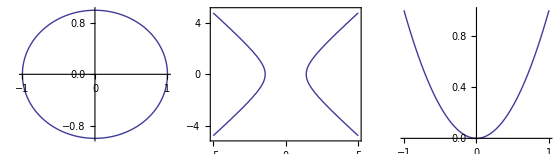

```mathematica
(*楕円または円*)
cc1=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi}];
(*双曲線*)
cc2=ContourPlot[x^2/2-y^2/2==1,{x,-5,5},{y,-5,5}];
(*放物線*)
cc3=Plot[x^2,{x,-1,1}];
GraphicsGrid[{{cc1,cc2,cc3}}]
```

## 2次曲線の行列表示

2次曲線 a x^2 + b y^2 + 2c xy + 2d x + 2e y + f = 0 は

(x | y)(a | c
c | b)(x
y)   + 2 (d | e)(x
y)  + f = 0

または

(x | y | 1)(a | c | d
c | b | e
d | e |  f)(x
y
1)  = 0

とベクトルと行列を用いて表すことができる．

2次曲線の分類 ⟺行列 (a | c
c | b) の分類 ⟺ 行列 (a | c
c | b) の固有値 で分類

これについては「直交変換と平行移動」 「座標の変換」 を勉強した後，もう少し詳しく説明します．

◀     |     ▶

## 2次曲線 = 円錐曲線

```mathematica
R[θ_]:=({{1, 0, 0}, {0, Cos[θ], -Sin[θ]}, {0, Sin[θ], Cos[θ]}});
Manipulate[
Show[
(*z軸*)
Graphics3D[Arrow[{{0,0,-2},{0,0,3}}]],
(*円錐*)
ParametricPlot3D[R[s].{r*Cos[t],r*Sin[t],1.5*r}+{0,0,l},{r,-1,1},{t,0,2*Pi}],
(*平面*)
Plot3D[0,{x,-2,2},{y,-2,2},PlotRange->All]
],
{{l,0,"円錐の頂点の位置"},0,1},
{{s,0,"円錐の回転角"},0,Pi}]
```

◀     |     ▶